```mathematica
Fitness[q_,nu_,qs_]:=If [nu≠Infinity,Exp[(1/nu) Cos[2 Pi q- 2 Pi qs]]/( BesselI[0,1/nu]),1];
```

```mathematica
a = 0.5;
Q =0.25;
μ = 0.2;
qs = 0.5;
 
g[x_,nu_] :=Q a x/μ NIntegrate[ Fitness[qq, nu, qs]/(μ + a x Fitness[qq,nu,qs]),{qq,0,1}]
```

# Coexistence between generalist and specialits.

## Using NDSolve in Mathematica for the von Mises fitness

```mathematica
(* Contains the dynamics of empty resources *)MeanField[com_,other_]:=Module[{NSP,B,μ,nstep,qstep,QQ,TMAX,aa,oldfitn,fitn,initialE,initialO, fE,fO,systemE,systemO,Fullsystem,variableE,variableO,Fullvariable,Solution, Result0,Result1,finalResult},
(* This is the parameter for species*)

NSP =Length[com];
(*
com[[i]] ={qS,nu, a};
land = {Qbar = B, mu, nqstep,TMAX}
*)

B = other[[1]];
μ = other[[2]];
nstep = other[[3]];
qstep = 1./nstep; QQ = Range[qstep,1,qstep];
TMAX = other[[4]];

aa= com[[All,3]];
Fitness[q_,spd_]:=If [spd[[2]]==Infinity,1. ,Exp[Cos[2 Pi (q- spd[[1]])]/spd[[2]]]/ BesselI[0,1/spd[[2]]]];

oldfitn =Table[Fitness[q, com[[sp]]],{sp,NSP},{q,QQ}];

fitn = Table[oldfitn[[sp]]/(qstep Total[oldfitn[[sp]]]),{sp,NSP}];
 (*Because of the discretization, the total fitness can be different, just renormalize here*)

(* Setting initial condition*)

initialE= Table[ρE[q][0]==0.1*B/μ,{q,QQ}];
initialO= Table[ρ[sp,q][0]== 0.9B/(μ NSP),{sp,NSP},{q,QQ}]; (* we assume 10 percent is empty, the rest ,90% is divided equally among the other species*)

(*This function calculates the change in abundance of resources of type q at time t that is empty (not occupied) *)
fE[q_,t_]:= B- μ* ρE[q][t]- ρE[q][t]* Sum[aa[[sp]]*fitn[[sp,Round[q/qstep]]]*  qstep* Sum[ρ[sp,qq][t],{qq,QQ}],{sp,NSP}];

(*This function calculates the change in the abundance of resources of type q at time t  that is occupied by species sp*)
fO[sp_,q_,t_]:=-μ * ρ[sp,q][t]+ρE[q][t]* aa[[sp]]*fitn[[sp,Round[q/qstep]]]* qstep*Sum[ρ[sp,qq][t],{qq,QQ}];


systemE=Table[ρE[q]'[t]==fE[q,t],{q,QQ}];
systemO=Table[ρ[sp,q]'[t]==fO[sp,q,t],{sp,NSP},{q,QQ}];

Fullsystem=Flatten[{systemE,systemO,initialE,initialO}];

variableE=Table[ρE[q],{q,QQ}];
variableO=Table[ρ[sp,q],{sp,NSP},{q,QQ}];

Fullvariable=Flatten[{variableE,variableO}];

Solution=NDSolve[Fullsystem,Fullvariable,{t,0,TMAX}];

(*This one is for the abundance at the middle of the simulation*)
Result0=Evaluate[Table[ρ[sp,q][TMAX/2.],{sp,NSP},{q,QQ}] /.Solution];

(*This one is for the abundance at the end of the simulation*)
Result1=Evaluate[Table[ρ[sp,q][TMAX],{sp,NSP},{q,QQ}] /.Solution];

finalResult= {Flatten[Result0,1],Flatten[Result1,1]}; 
finalResult]
```

```mathematica
(*TRYING TO MAKE THE CODE FASTER BY REMOVING RESOURCE DYNAMCS*)MeanField2[com_,other_]:=Module[{NSP,B,μ,nstep,qstep,QQ,TMAX,aa,oldfitn,fitn,initialE,initialO, fE,fO,systemE,systemO,Fullsystem,variableE,variableO,Fullvariable,Solution, Result0,Result1,finalResult},
(* This is the parameter for species*)

NSP =Length[com];
(*
com[[i]] ={qS,nu, a};
land = {Qbar = B, mu, nqstep,TMAX}
*)

B = other[[1]];
μ = other[[2]];
nstep = other[[3]];
qstep = 1./nstep; QQ = Range[qstep,1,qstep];
TMAX = other[[4]];

aa= com[[All,3]];
Fitness[q_,spd_]:=If [spd[[2]]==Infinity,1. ,Exp[Cos[2 Pi (q- spd[[1]])]/spd[[2]]]/ BesselI[0,1/spd[[2]]]];

oldfitn =Table[Fitness[q, com[[sp]]],{sp,NSP},{q,QQ}];

fitn = Table[oldfitn[[sp]]/(qstep Total[oldfitn[[sp]]]),{sp,NSP}];
 (*Because of the discretization, the total fitness can be different, just renormalize here*)

(* Setting initial condition*)

(*initialE= Table[ρE[q][0]==0.1*B/μ,{q,QQ}];*)
initialO= Table[ρ[sp,q][0]== 0.9B/(μ NSP),{sp,NSP},{q,QQ}]; (* we assume 10 percent is empty, the rest ,90% is divided equally among the other species*)

(*This function calculates the change in abundance of resources of type q at time t that is empty (not occupied) *)
(*fE[q_,t_]:= B- μ* ρE[q][t]- ρE[q][t]* Sum[aa[[sp]]*fitn[[sp,Round[q/qstep]]]*  qstep* Sum[ρ[sp,qq][t],{qq,QQ}],{sp,NSP}];*)

(*This function calculates the change in the abundance of resources of type q at time t  that is occupied by species sp*)
fO[sp_,q_,t_]:=-μ * ρ[sp,q][t]+(B/μ - Sum[ρ[ssp,q][t],{ssp,NSP}])* aa[[sp]]*fitn[[sp,Round[q/qstep]]]* qstep*Sum[ρ[sp,qq][t],{qq,QQ}];


(*systemE=Table[ρE[q]'[t]==fE[q,t],{q,QQ}];*)
systemO=Table[ρ[sp,q]'[t]==fO[sp,q,t],{sp,NSP},{q,QQ}];

Fullsystem=Flatten[{(*systemE,*)systemO,(*initialE,*)initialO}];

(*variableE=Table[ρE[q],{q,QQ}];*)
variableO=Table[ρ[sp,q],{sp,NSP},{q,QQ}];

Fullvariable=Flatten[{(*variableE,*)variableO}];

Solution=NDSolve[Fullsystem,Fullvariable,{t,0,TMAX}];

(*This one is for the abundance at the middle of the simulation*)
Result0=Evaluate[Table[ρ[sp,q][TMAX/2.],{sp,NSP},{q,QQ}] /.Solution];

(*This one is for the abundance at the end of the simulation*)
Result1=Evaluate[Table[ρ[sp,q][TMAX],{sp,NSP},{q,QQ}] /.Solution];

finalResult= {Flatten[Result0,1],Flatten[Result1,1]}; 
finalResult]
```

```mathematica
localdir = "C:\\Users\\tramiada\\Documents\\Projects\\coexistence\\sim3\\";  qS1 = 0.25; qS2= 0.75; as =0.5;
NU= Flatten[{Subdivide[0.05,2,50],4,8,16}];
```

```mathematica
time1= AbsoluteTiming[
Do[
OTHER ={B ,μ = 0.1,NSTEP=100,TMAX = 2000};
middata= enddata= {};
Do[
com1= {qS1,ν,as};
com2 = {qS2 ,ν, as};
com3 = {0.5 ,Infinity, pag as};
COM = {com1,com2,com3};
data = MeanField2[COM,OTHER];

data1 = data[[1]]; (*this is prevelance at the middle of the simulation*)
data2= data[[2]];  (*this is prevelance at the end of the simulation*)

PrependTo[data1,ν];
PrependTo[data2,ν];

AppendTo[middata, data1];
AppendTo[enddata, data2];
,{ν,NU}];
Export[localdir<>"2spe_1gen_midTMAX_NSTEP_"<>ToString@NSTEP<>"_B_"<>ToString@B<>"_pas_"<>ToString@pag<>".csv",middata];
Export[localdir<>"2spe_1gen_endTMAX_NSTEP_"<>ToString@NSTEP<>"_B_"<>ToString@B<>"_pas_"<>ToString@pag<>".csv",enddata];
,{pag, Subdivide[0.1,0.95,1]},{B,{2}}];
]; (* about 11 min*)


time2= AbsoluteTiming[
Do[
OTHER ={B ,μ = 0.1,NSTEP=100,TMAX = 2000};
middata= enddata= {};
Do[
com1= {qS1,ν,as};
com2 = {qS2 ,ν, as};
com3 = {0.5 ,Infinity, pag as};
com4 = {0.5 ,Infinity, pag as};
COM = {com1,com2,com3,com4};
data = MeanField2[COM,OTHER];

data1 = data[[1]]; (*this is prevelance at the middle of the simulation*)
data2= data[[2]];  (*this is prevelance at the end of the simulation*)

PrependTo[data1,ν];
PrependTo[data2,ν];

AppendTo[middata, data1];
AppendTo[enddata, data2];
,{ν,NU}];
Export[localdir<>"2spe_2gen_midTMAX_NSTEP_"<>ToString@NSTEP<>"_B_"<>ToString@B<>"_pas_"<>ToString@pag<>".csv",middata];
Export[localdir<>"2spe_2gen_endTMAX_NSTEP_"<>ToString@NSTEP<>"_B_"<>ToString@B<>"_pas_"<>ToString@pag<>".csv",enddata];
,{pag,Subdivide[0.1,0.95,50]},{B,{2}}];
]; 

qS1 = 1./3; qS2 = 2./3; qS3 = 1.;
time3= AbsoluteTiming[
Do[
OTHER ={B ,μ = 0.1,NSTEP=100,TMAX = 2000}; 
middata= enddata= {};
Do[
com1= {qS1,ν,as};
com2 = {qS2 ,ν, as};
com3 = {qS3 ,ν, as};
com4 = {0.5 ,Infinity, pag as};
COM = {com1,com2,com3,com4};
data = MeanField2[COM,OTHER];

data1 = data[[1]]; (*this is prevelance at the middle of the simulation*)
data2= data[[2]];  (*this is prevelance at the end of the simulation*)

PrependTo[data1,ν];
PrependTo[data2,ν];

AppendTo[middata, data1];
AppendTo[enddata, data2];
,{ν,NU}];
Export[localdir<>"3spe_1gen_midTMAX_NSTEP_"<>ToString@NSTEP<>"_B_"<>ToString@B<>"_pas_"<>ToString@pag<>".csv",middata];
Export[localdir<>"3spe_1gen_endTMAX_NSTEP_"<>ToString@NSTEP<>"_B_"<>ToString@B<>"_pas_"<>ToString@pag<>".csv",enddata];
,{pag,Subdivide[0.1,0.95,50]},{B,{2}}];
];
```

$Aborted

$Aborted

### Plotting coexistence as a function of nu and colonization rate

```mathematica
localdir = "C:\\Users\\tramiada\\Documents\\Projects\\coexistence\\sim3\\";
```

```mathematica
(*  2 specialists and 1 generalist *)

OTHER ={B ,μ = 0.1,NSTEP=100,TMAX = 2000};

result1 = {};
Do[
data = ToExpression@Import[localdir<>"2spe_1gen_midTMAX_NSTEP_"<>ToString@NSTEP<>"_B_"<>ToString@B<>"_pas_"<>ToString@pag<>".csv"];

Do[
subd = data[[l]];
nu  = subd[[1]];
occ = Map[Total,subd[[2;;]]]/NSTEP  μ/B;
binaryocc = If[occ[[-1]] >0.00001, 1, 0.];
AppendTo[result1, Chop@Flatten@{pag,Log@nu,binaryocc}];
,{l,Length[data]-2}];

,{pag,Subdivide[0.1,0.95,50]},{B,{2}}];

OTHER ={B ,μ = 0.1,NSTEP=100,TMAX = 2000};

result2 = {};
Do[
data = ToExpression@Import[localdir<>"2spe_1gen_endTMAX_NSTEP_"<>ToString@NSTEP<>"_B_"<>ToString@B<>"_pas_"<>ToString@pag<>".csv"];

Do[
subd = data[[l]];
nu  = subd[[1]];
occ = Map[Total,subd[[2;;]]]/NSTEP  μ/B;
binaryocc = If[occ[[-1]] >0.00001, 1, 0.];
AppendTo[result2, Chop@Flatten@{pag,Log@nu,binaryocc}];
,{l,Length[data]-2}];

,{pag,Subdivide[0.1,0.95,50]},{B,{2}}];
```

```mathematica
fig1 = Labeled[ListDensityPlot[result1,ColorFunction-> GrayLevel, FrameStyle->as],{"ag/as","Log(ν)", "mid"},{Bottom,Left,Top},RotateLabel-> True,LabelStyle->ls, Spacings->{0.2,0.2}];

fig2 = Labeled[ListDensityPlot[result2,ColorFunction-> GrayLevel, FrameStyle->as],{"ag/as","Log(ν)", "final"},{Bottom,Left,Top},RotateLabel-> True,LabelStyle->ls, Spacings->{0.2,0.2}];


F1 = Grid[{{fig1,fig2}},Spacings->{0.4,0.4}];
```

```mathematica
(*  3 specialists and 1 generalist *)

OTHER ={B ,μ = 0.1,NSTEP=100,TMAX = 2000};

result3 = {};
Do[
data = ToExpression@Import[localdir<>"3spe_1gen_midTMAX_NSTEP_"<>ToString@NSTEP<>"_B_"<>ToString@B<>"_pas_"<>ToString@pag<>".csv"];

Do[
subd = data[[l]];
nu  = subd[[1]];
occ = Map[Total,subd[[2;;]]]/NSTEP  μ/B;
binaryocc = If[occ[[-1]] >0.00001, 1, 0.];
AppendTo[result3, Chop@Flatten@{pag,Log@nu,binaryocc}];
,{l,Length[data]-2}];

,{pag,Subdivide[0.1,0.95,50]},{B,{2}}];

OTHER ={B ,μ = 0.1,NSTEP=100,TMAX = 2000};

result4 = {};
Do[
data = ToExpression@Import[localdir<>"3spe_1gen_endTMAX_NSTEP_"<>ToString@NSTEP<>"_B_"<>ToString@B<>"_pas_"<>ToString@pag<>".csv"];

Do[
subd = data[[l]];
nu  = subd[[1]];
occ = Map[Total,subd[[2;;]]]/NSTEP  μ/B;
binaryocc = If[occ[[-1]] >0.00001, 1, 0.];
AppendTo[result4, Chop@Flatten@{pag,Log@nu,binaryocc}];
,{l,Length[data]-2}];

,{pag,Subdivide[0.1,0.95,50]},{B,{2}}];
```

```mathematica
fig3 = Labeled[ListDensityPlot[result3,ColorFunction-> GrayLevel, FrameStyle->as],{"ag/as","Log(ν)", "mid"},{Bottom,Left,Top},RotateLabel-> True,LabelStyle->ls, Spacings->{0.2,0.2}];

fig4 = Labeled[ListDensityPlot[result4,ColorFunction-> GrayLevel, FrameStyle->as],{"ag/as","Log(ν)", "final"},{Bottom,Left,Top},RotateLabel-> True,LabelStyle->ls, Spacings->{0.2,0.2}];

F2 = Grid[{{fig3,fig4}}];
```

```mathematica
(*  2 specialists and 2 generalist *)

OTHER ={B ,μ = 0.1,NSTEP=100,TMAX = 2000};

result5 = {};
Do[
data = ToExpression@Import[localdir<>"2spe_2gen_midTMAX_NSTEP_"<>ToString@NSTEP<>"_B_"<>ToString@B<>"_pas_"<>ToString@pag<>".csv"];

Do[
subd = data[[l]];
nu  = subd[[1]];
occ = Map[Total,subd[[2;;]]]/NSTEP  μ/B;
binaryocc1 = If[occ[[-2]] >0.00001, 1, 0.];
binaryocc2 = If[occ[[-1]] >0.00001, 1, 0.];
AppendTo[result5, Chop@Flatten@{pag,Log@nu,binaryocc1,binaryocc2}];
,{l,Length[data]-2}];

,{pag,Subdivide[0.1,0.95,50]},{B,{2}}];

OTHER ={B ,μ = 0.1,NSTEP=100,TMAX = 2000};

result6 = {};
Do[
data = ToExpression@Import[localdir<>"2spe_2gen_endTMAX_NSTEP_"<>ToString@NSTEP<>"_B_"<>ToString@B<>"_pas_"<>ToString@pag<>".csv"];

Do[
subd = data[[l]];
nu  = subd[[1]];
occ = Map[Total,subd[[2;;]]]/NSTEP  μ/B;
binaryocc1 = If[occ[[-2]] >0.00001, 1, 0.];
binaryocc2 = If[occ[[-1]] >0.00001, 1, 0.];
AppendTo[result6, Chop@Flatten@{pag,Log@nu,binaryocc1,binaryocc2}];
,{l,Length[data]-2}];

,{pag,Subdivide[0.1,0.95,50]},{B,{2}}];
```

```mathematica
fig51 = Labeled[ListDensityPlot[result5[[All,{1,2,3}]],ColorFunction-> GrayLevel, FrameStyle->as],{"ag/as","Log(ν)", "mid_g1"},{Bottom,Left,Top},RotateLabel-> True,LabelStyle->ls, Spacings->{0.2,0.2}];

fig52 = Labeled[ListDensityPlot[result5[[All,{1,2,4}]],ColorFunction-> GrayLevel, FrameStyle->as],{"ag/as","Log(ν)", "mid_g2"},{Bottom,Left,Top},RotateLabel-> True,LabelStyle->ls, Spacings->{0.2,0.2}];

fig61 = Labeled[ListDensityPlot[result6[[All,{1,2,3}]],ColorFunction-> GrayLevel, FrameStyle->as],{"ag/as","Log(ν)", "final_g1"},{Bottom,Left,Top},RotateLabel-> True,LabelStyle->ls, Spacings->{0.2,0.2}];

fig62 = Labeled[ListDensityPlot[result5[[All,{1,2,4}]],ColorFunction-> GrayLevel, FrameStyle->as],{"ag/as","Log(ν)", "final_g2"},{Bottom,Left,Top},RotateLabel-> True,LabelStyle->ls, Spacings->{0.2,0.2}];

F3 = Grid[Transpose@{{fig51,fig52},{fig61,fig62}},Spacings->{2,2}];
```

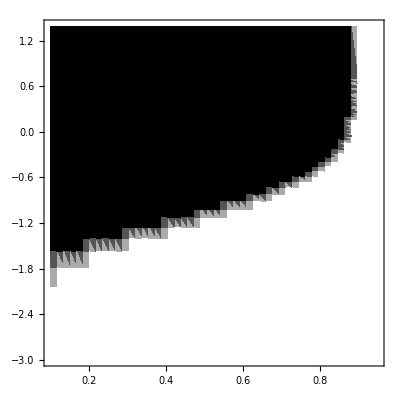
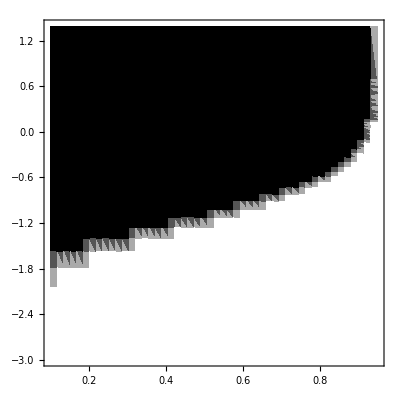
-Graphics-ag/asLog(ν)mid | -Graphics-ag/asLog(ν)final

```mathematica
F1
```

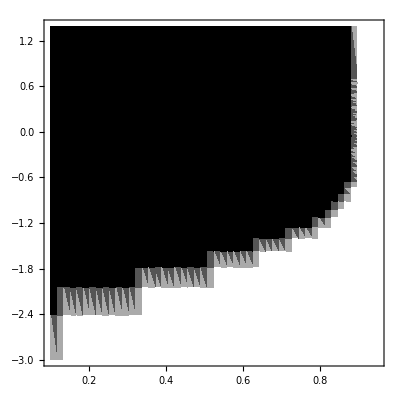
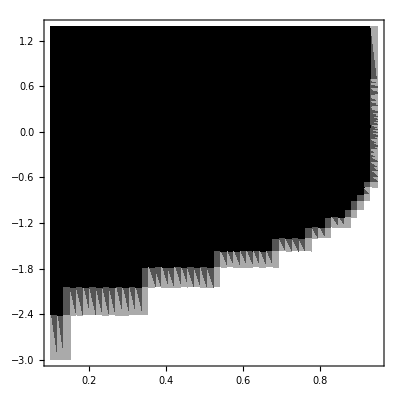
-Graphics-ag/asLog(ν)mid | -Graphics-ag/asLog(ν)final

```mathematica
F2
```

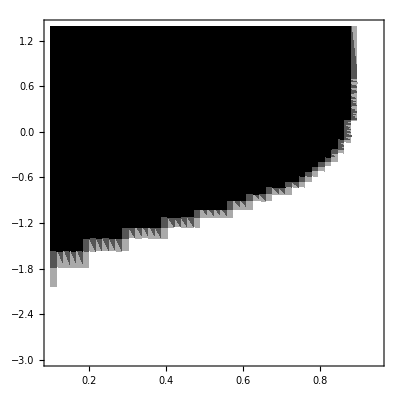
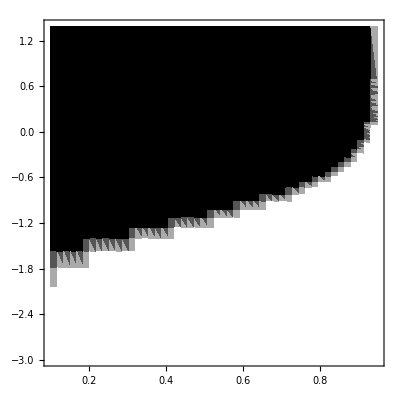
-Graphics-ag/asLog(ν)mid_g1 | -Graphics-ag/asLog(ν)final_g1
-Graphics-ag/asLog(ν)mid_g2 | -Graphics-ag/asLog(ν)final_g2

```mathematica
F3
```

```mathematica
Export[localdir<>"2spe_2gen.jpeg",F3,ImageResolution->100];
Export[localdir<>"3spe_1gen.jpeg",F2,ImageResolution->100];
Export[localdir<>"2spe_1gen.jpeg",F1,ImageResolution->100];
```

#### For fixed ag

```mathematica
localdir = "C:\\Users\\tramiada\\Documents\\Projects\\coexistence\\sim2\\";
```

```mathematica
as= 0.5;
AG  =as Subdivide[0.1,0.95,5];
OTHER ={B = 1,μ = 0.1,NSTEP=100,TMAX = 2000};
```

```mathematica
FIG ={};
Do[
data0= ToExpression@Import[localdir<>"midTMAX_NSTEP_"<>ToString@NSTEP<>"_B_"<>ToString@B<>"_ag_"<>ToString@ag<>".csv"];

data1= ToExpression@Import[localdir<>"endTMAX_NSTEP_"<>ToString@NSTEP<>"_B_"<>ToString@B<>"_ag_"<>ToString@ag<>".csv"];
FIG= {};
Do[

dd = data0[[i]];
sp1 = Transpose[{Subdivide[0.,1,NSTEP-1],dd[[2]]}];
sp2 = Transpose[{Subdivide[0.,1,NSTEP-1],dd[[3]]}];
sp3 = Transpose[{Subdivide[0.,1,NSTEP-1],dd[[4]]}];

ee = data1[[i]];
sp1f = Transpose[{Subdivide[0.,1,NSTEP-1],ee[[2]]}];
sp2f = Transpose[{Subdivide[0.,1,NSTEP-1],ee[[3]]}];
sp3f = Transpose[{Subdivide[0.,1,NSTEP-1],ee[[4]]}];
fig =Labeled[ListLinePlot[{sp1,sp2,sp3,sp1f,sp2f,sp3f},PlotStyle->{Pink,Cyan,{Black,Dashed},Red,Blue,{Gray,Dashed}},PlotRange->{All,{0,B/μ}}],ToString@dd[[1]], Top];
AppendTo[FIG,fig];
,{i,Length[NU]}];

,{ag,{AG[[5]]}}];
```

```mathematica
Manipulate[FIG[[i]],{i,1,Length[NU],1}]
```

Part::partd: Part specification FIG ⟦ 7 ⟧ is longer than depth of object.

Part::partw: Part 7 of {} does not exist.

Part::partd: Part specification FIG ⟦ 54 ⟧ is longer than depth of object.

```mathematica
as= 0.5;
AG  =as Subdivide[0.1,0.95,5];
OTHER ={B = 4,μ = 0.1,NSTEP=100,TMAX = 2000};
```

```mathematica
FIG2 ={};
Do[
data0= ToExpression@Import[localdir<>"midTMAX_NSTEP_"<>ToString@NSTEP<>"_B_"<>ToString@B<>"_ag_"<>ToString@ag<>".csv"];

data1= ToExpression@Import[localdir<>"endTMAX_NSTEP_"<>ToString@NSTEP<>"_B_"<>ToString@B<>"_ag_"<>ToString@ag<>".csv"];
FIG= {};
Do[

dd = data0[[i]];
sp1 = Transpose[{Subdivide[0.,1,NSTEP-1],dd[[2]]}];
sp2 = Transpose[{Subdivide[0.,1,NSTEP-1],dd[[3]]}];
sp3 = Transpose[{Subdivide[0.,1,NSTEP-1],dd[[4]]}];

ee = data1[[i]];
sp1f = Transpose[{Subdivide[0.,1,NSTEP-1],ee[[2]]}];
sp2f = Transpose[{Subdivide[0.,1,NSTEP-1],ee[[3]]}];
sp3f = Transpose[{Subdivide[0.,1,NSTEP-1],ee[[4]]}];
fig =Labeled[ListLinePlot[{sp1,sp2,sp3,sp1f,sp2f,sp3f},PlotStyle->{Pink,Cyan,{Black,Dashed},Red,Blue,{Gray,Dashed}},PlotRange->{All,{0,B/μ}}],ToString@dd[[1]], Top];
AppendTo[FIG2,fig];
,{i,Length[NU]}];

,{ag,{AG[[5]]}}];
```

```mathematica
Manipulate[FIG2[[i]],{i,1,Length[NU],1}]
```

Part::partd: Part specification FIG2 ⟦ 7 ⟧ is longer than depth of object.

```mathematica
FIG ={};Do[data0= ToExpression@Import["C:\\Users\\tramiada\\Documents\\Projects\\coexistence\\sim2\\midTMAX_NSTEP_100_ag_"<>ToString@ag<>".csv"];

data1= ToExpression@Import["C:\\Users\\tramiada\\Documents\\Projects\\coexistence\\sim2\\endTMAX_NSTEP_100_ag_"<>ToString@ag<>".csv"];

dd = data0[[50]];
sp1 = Transpose[{Subdivide[0.,1,99],dd[[2]]}];
sp2 = Transpose[{Subdivide[0.,1,99],dd[[3]]}];
sp3 = Transpose[{Subdivide[0.,1,99],dd[[4]]}];

ee = data1[[50]];
sp1f = Transpose[{Subdivide[0.,1,99],ee[[2]]}];
sp2f = Transpose[{Subdivide[0.,1,99],ee[[3]]}];
sp3f = Transpose[{Subdivide[0.,1,99],ee[[4]]}];
fig =Labeled[ListLinePlot[{sp1,sp2,sp3,sp1f,sp2f,sp3f},PlotStyle->{Pink,Cyan,{Black,Dashed},Red,Blue,{Gray,Dashed}},PlotRange->{All,{0,B/μ}}],ToString@ag, Top];

AppendTo[FIG,fig];

,{ag,as Subdivide[0.1,0.95,10]}];
```

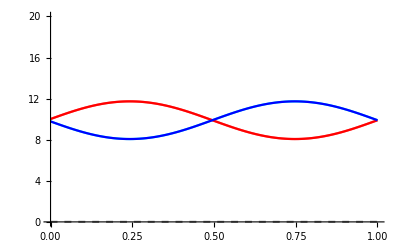
{-Graphics-0.05,-Graphics-0.0925,-Graphics-0.135,-Graphics-0.1775,-Graphics-0.22,-Graphics-0.2625,-Graphics-0.305,-Graphics-0.3475,-Graphics-0.39,-Graphics-0.4325,-Graphics-0.475}

```mathematica
FIG
```